## Supporting numerics for SM Section I

This is the Mathematica script used to generate Panels B and C of Suppl.Fig.5.

It is used to numerically solve for the steady-state probability of any give EcR being found in one of its accessible complexes. These probabilities are subsequently related to the modulation of transcriptional activity at a qualitative level via the modulation factor defined in Eq.(S23). A detailed derivation of the corresponding mathematical expressions can be found in SM Section I.

```mathematica
(*First, use Eqs.(S13) and (S18) to write*)
EcRlbd = EcR (EcRtotlbd/EcRtot);
EcRr = κR Rf EcR;
EcRe = κE Ecf EcR;
EcRea = κA κE Af Ecf EcR;
EcRrlbd = κR Rf EcRlbd;
EcRelbd = κE Ecf EcRlbd;
EcRealbd = κA κE Af Ecf EcRlbd;

(*Then, using (S14-S16), write Eq.(S17)in such a way that it only depends on total concentrations and affinities
which are here taken to be the free parameters of the model. The relation EQ1 - equivalent to Eq.(S17)- will be solved numerically for all parameter choices of interest.*)
a =  κE κA(EcR + EcRlbd) Atot;
b = -(+ κE κA (EcR + EcRlbd) Atot - (1+ κE(EcR + EcRlbd))- κE κA Ectot (EcR + EcRlbd));
c = -(1 + κE (EcR + EcRlbd));
ϕA = (-b + Sqrt[b^2 - 4 a c])/(2a) ;
Af = ϕA* Atot;
Ecf = (1-ϕA)/(ϕA κA κE (EcR + EcRlbd));
Rf = Rtot/(1 + κR(EcR + EcRlbd));
EQ1 = FullSimplify[EcRtot == EcR(1 + κR Rf + κE Ecf + κA κE Af Ecf)];

(*Steady-state concentration of free EcR*)
EcRSS[pκA_,pκE_,pκR_,pEcRtot_,pEcRtotlbd_,pAtot_,pRtot_,pEctot_] :=(EcR/pEcRtot) /. FindRoot[EQ1  /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot},{EcR,0.001pEcRtot }] /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot}

(*Steady-state concentration of EcRe complex*)
EcReSS[pκA_,pκE_,pκR_,pEcRtot_,pEcRtotlbd_,pAtot_,pRtot_,pEctot_] :=(EcRe/pEcRtot) /. FindRoot[EQ1  /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot},{EcR,0.001pEcRtot }] /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot}

(*Steady-state concentration of EcRea complex*)
EcReaSS[pκA_,pκE_,pκR_,pEcRtot_,pEcRtotlbd_,pAtot_,pRtot_,pEctot_] :=(EcRea/pEcRtot) /. FindRoot[EQ1  /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot},{EcR,0.001pEcRtot }] /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot}

(*Steady-state concentration of EcRr complex*)
EcRrSS[pκA_,pκE_,pκR_,pEcRtot_,pEcRtotlbd_,pAtot_,pRtot_,pEctot_] :=(EcRr/pEcRtot) /. FindRoot[EQ1  /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot},{EcR,0.001pEcRtot }] /. {κA->pκA,κE->pκE,κR->pκR,EcRtot->pEcRtot,EcRtotlbd->pEcRtotlbd,Atot->pAtot,Rtot->pRtot,Ectot->pEctot}
```

The expressions written above are now used to calculate the probability of EcR being found in each of the available complexes as a function of total 20E and EcR concentration. All other parameters are kept fixed (in particular, we impose that the concentration of the diffusible EcR fragment is zero).

1/60

1/60

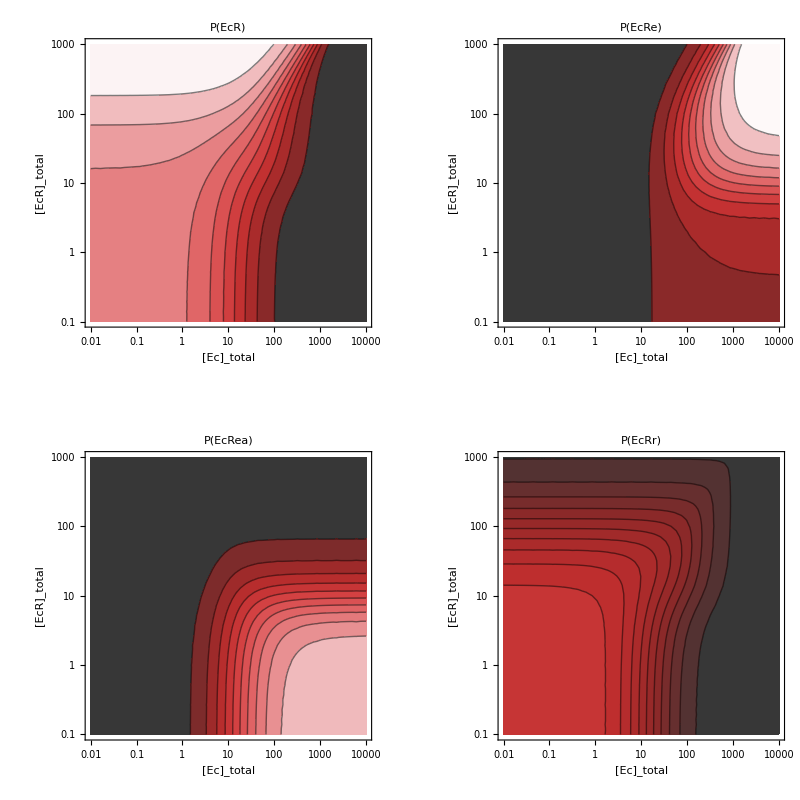

```mathematica
kec = 1/60;
ksm = 1/60;

p1 =ContourPlot[EcRSS[1,kec,ksm,y,0,5,30,x],{x,0.01,10000},{y,0.1,1000},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->ColorData[{"CherryTones",{0,1}}],ColorFunctionScaling->False,ScalingFunctions->{"Log","Log"},PlotLabel->"P(EcR)"];
p2 = ContourPlot[EcReSS[1,kec,ksm,y,0,5,30,x],{x,0.01,10000},{y,0.1,1000},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->ColorData[{"CherryTones",{0,1}}],ColorFunctionScaling->False,ScalingFunctions->{"Log","Log"},PlotLabel->"P(EcRe)"];
p3 = ContourPlot[EcReaSS[1,kec,ksm,y,0,5,30,x],{x,0.01,10000},{y,0.1,1000},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->ColorData[{"CherryTones",{0,1}}],ColorFunctionScaling->False,ScalingFunctions->{"Log","Log"},PlotLabel->"P(EcRea)"];
p4 = ContourPlot[EcRrSS[1,kec,ksm,y,0,5,30,x],{x,0.01,10000},{y,0.1,1000},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->ColorData[{"CherryTones",{0,1}}],ColorFunctionScaling->False,ScalingFunctions->{"Log","Log"},PlotLabel->"P(EcRr)"];
Legended[GraphicsGrid[{{p1,p2},{p3,p4}},Frame->False],BarLegend[{"CherryTones",{0,1}},10]]
```

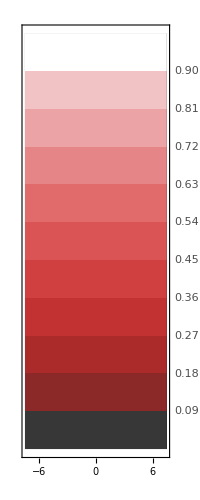
```mathematica
-Graphics--Graphics-
```

In order to qualitatively link the probabilities calculate above to a modulation of target transcription, we compute the context-dependent “modulator factor” introduced in Eq.(S23). First, this is calculated at zero EcR fragment concentration (varying the total 20E and EcR levels) and consequently at fixed EcR concentration EcR_tot=5 nM (varying the total 20E and EcR fragment levels). Note that EcR complexes are assumed to only affect transcription when they are bound to DNA in proximity of the ERE, thus the probability of a EcR being in a given complex needs to be multiplied by the probability of an ERE of interest being occupied by EcR, Eq.(S22).

```mathematica
(*Calculate probability of arbitrary DNA binding domain being occupied by an EcR*)
PDBDb[pκD_,pEcRtot_,pDBDtot_]:= PB /. NSolve[{PB == pκD(pEcRtot-PB pDBDtot)/(1 + pκD(pEcRtot-PB pDBDtot)),0<=PB<=1},PB]

kec = 1/60;
ksm = 1/60;

newStyle[x_]:=x/. l_Line:>Sequence[Opacity[.4],Thick,Dashed,Black,l]
p1 = ContourPlot[(EcReaSS[1,kec,ksm,y,0,5,30,x]-EcRrSS[0.5,kec,ksm,y,0,5,30,x])PDBDb[20,y,1],{x,0.1,10000},{y,0.1,100},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->"CherryTones",ScalingFunctions->{"Log","Log"},PlotLegends->Automatic]/. Tooltip[x_,0]:>Tooltip[newStyle[x],0];
p2 = ContourPlot[(EcReaSS[1,kec,ksm,5,y,5,30,x]-EcRrSS[1,kec,ksm,5,y,5,30,x])PDBDb[20,5,1],{x,0.01,10000},{y,0.1,1000},FrameLabel->{"[Ec]_total","[EcR]_total"},PlotRange->All,Contours->10,ColorFunction->"CherryTones",ScalingFunctions->{"Log","Log"},PlotLegends->Automatic]/. Tooltip[x_,0]:>Tooltip[newStyle[x],0];
GraphicsGrid[{{p1,p2}},Frame->False]
```

1/60

1/60

-Graphics-